## Erro, instância erroMDE, geraEsferas

```mathematica
(* módulo erro *)
erroMDE[x_,A_,d_,m_]:=Module[{MDE,ii},
MDE=0;
For[ii=1,ii≤m,ii++,
MDE=MDE+(1/d[[ii,1]])*Abs[Norm[x-A[[;;,ii]]]-d[[ii,1]]];
];
MDE=(1/m)*MDE;
Return[MDE];
];
```

```mathematica
(* gera matriz nxm de rank k, cujas colunas 
são os centros das m esferas; gera vetor com os raios
 *)
geraEsferas[m_,n_,kk_, seed_:1]:=Module[{A,ii,d,lambda,u,v,Amin,Amax,xstar,di},
A=Table[0,{ii,n},{jj,m}];d=Table[0,{ii,m},{jj,1}];
lambda = 0; u = Table[0,{ii,n}]; v = Table[0,{ii,m}];
For[ii=1,ii≤kk,ii++,
(*Print[">> seed = ", seed];*)
If[seed == 1,
SeedRandom[ii];lambda=RandomReal[{0,10}];
SeedRandom[ii+1];u=RandomReal[{0,1},n];
SeedRandom[ii+2];v=RandomReal[{0,1},m];
(*Print[">> ii = ", Style[ii,Red], " lambda = ", Style[lambda,Red],  " u = ", Style[u,Red], " v = ", Style[v,Red]];*)
,
lambda=RandomReal[{0,10}];
u=RandomReal[{0,1},n];
v=RandomReal[{0,1},m];
(*Print[">> OK"];*)
];
A=A+lambda*Outer[Times,u,v];
];
Amin=Min[A];Amax=Max[A];
If[seed == 1,
SeedRandom[42];xstar=RandomReal[{Amin,Amax},n];
(*Print[">> xstar = ", Style[xstar,Red]];*)
,
xstar=RandomReal[{Amin,Amax},n];
];
For[ii=1,ii≤m,ii++,
di=Norm[xstar-A[[;;,ii]]];
d[[ii,1]]=di;
(*Print[">> di = ", Style[di,Red]];*)
];
Return[{A,d}];
];

(* decomposição QR *)
qrd[mat_?MatrixQ]:=Module[{r=mat,h,m,n,q,v},
{m,n}=Dimensions[r];q=IdentityMatrix[m];
Do[v=PadLeft[r[[kk;;,kk]],m];
h=ReflectionMatrix[v-SparseArray[{kk->Norm[v]},m]];
q=q.h;r=h.r,{kk,n}];
{q,r}
];
```

## Interseção de esferas IntersEsferas, IntersEsferasAGC

### Abordagem clássica

```mathematica
(* gera as esferas e computa interseção via álgebra linear *)
IntersEsferas[n_,m_,kk_,verbose_:True]:=Module[{A,d,Â,ii,jj,Q,R,c,cbar,Rhat,Rhat1,c1,Rhat2,c2,y,del,z,w,x1,x2,z1,z2,w1,w2,erro,aux,z0},

(* gera esferas *)
{A,d}=geraEsferas[m,n,kk];
If[verbose,
(*Print["A = ",MatrixForm[A],"  d = ",MatrixForm[d],", rank(A) = ",MatrixRank[A]];*)(*calcula a matriz Â*)
Print["A = ",Style[MatrixForm[A],Red],"  d = ",Style[MatrixForm[d],Red]];
];

Â=Table[0,{ii,n},{jj,m-1}];
For[jj=1,jj≤m-1,jj++,
Â[[;;,jj]]=A[[;;,jj]]-A[[;;,m]];];
(*resolve o sistema Â^t xbar=c via decomposicao QR de Â*)
{Q,R}=qrd[Â];
(*computa vetor c*)
c=Table[0,{ii,m-1},{jj,1}];
cbar=Table[0,{ii,m-1},{jj,1}];
For[ii=1,ii≤m-1,ii++,
c[[ii,1]]=(-1/2)*(d[[ii,1]]^2-d[[m,1]]^2-Norm[Â[[;;,ii]]]^2);];
Rhat=R[[1;;kk,;;]];
Rhat1=Rhat[[;;,1;;kk]];
c1=c[[1;;kk,1]];
If[kk≠m-1,
Rhat2=Rhat[[;;,kk+1;;m-1]];
c2=c[[kk+1;;m-1,1]];
y=LinearSolve[Transpose[Rhat1],c1];
If[Norm[Transpose[Rhat2].y-c2]>10^(-6),
Print["y não pertence a imagem de Rhat^t"];
Print["Intersecao vazia"];
Return[{0,0}];
];
,y=LinearSolve[Transpose[Rhat],c];
];
(*computa argumento da raiz quadrada*)
del=d[[m,1]]^2-Norm[y]^2;
(*Print["δ = ",del];*)
If[del<0,Print["Intersecao vazia"];
Return[{0,0}];
];
If[del==0,z=0;
w=AppendTo[w,z];
x1=MatrixForm[Q.w+A[[;;,n]]];
x2=x1;
erro=erroMDE[x1,A,d,m];
(*Print["Solução: x = ",x1];*)
];
If[del>0,
If[n-kk>1,
Print["||z||^2 = ",del,", onde z∈R^(n-k), sendo n = ",n,",  k = ",kk];
Print["Conjunto solução:"];
Print["{ x∈R^n: x = Q[y z]^t + a_m, onde y = ",MatrixForm[y],",  a_m = ",MatrixForm[A[[;;,m]]],",  Q: ",n,"x",n," e z ∈ R^",n-kk," tal que ||z||^2 = ",del," }"];
(*escolhe z em R^n-k tq z^2=del^2=d_m^2-y^2*)
aux=RandomReal[{-del,del},n-kk];
z0=del/Norm[aux]*aux;
w=y;
For[ii=1,ii≤Length[z0],ii++,
w=AppendTo[w,w[[ii]]];
];
x1=Q.w+A[[;;,m]];
erro=erroMDE[x1,A,d,m];
Print["z0 = ",z0,", del = ",del,", erro = ",erro];
Print["||z0|| = ",Norm[z0]];
Print[" - - - - - - - - - "];,z1=Sqrt[del];
z2=-Sqrt[del];
w1=y;
w1=AppendTo[w1,{z1}];
w2=y;
w2=AppendTo[w2,{z2}];
x1=Q.w1+A[[;;,m]];
x2=Q.w2+A[[;;,m]];
erro=erroMDE[x1,A,d,m];
];
(*Print["Soluções: x1 = ",x1,",  x2 = ",x2];*)
];
(*Print["Erro de x1: ",erro];
Print["Erro de x2: ",erroMDE[x2,A,d,m]];*)(*Print[" - - - - - - - - - "];*)
Return[{m,erro}];
];
```

### Abordagem via AGC

```mathematica
(* carrega pacote clifford *)
<<"clifford.m"
```

```mathematica
(* módulo interseção usando AGC *)IntersEsferasAGC[n_,m_,kk_,e0_,einf_,verbose_:True]:=Module[{epsilon,p,A,d,ii,TEsferas,ri,Ci,ci,sigmai,sigma,a,aa,inva,sigmaN,a2,pto1,Ie,pto2,x1,x2,X,x,y,z,pp,eqSigma,erro},

epsilon=3;
p=n+1;

(* gera m esferas no R^n *)
{A,d}=geraEsferas[m,n,kk];

If[verbose,
Print["A = ",Style[MatrixForm[A],Red], ",  d = ",Style[MatrixForm[d],Red]];
];

(* define esferas no espaço conforme *)
TEsferas={};
For[ii=1,ii≤m,ii++,
ri=d[[ii,1]];Ci=ToBasis[A[[;;,ii]]];
ci=e0+Ci+(0.5*Norm[ToVector[Ci,p+1]]^2)*einf;
sigmai=ci-(0.5*ri^2)*einf;
TEsferas=AppendTo[TEsferas,sigmai];
];

(*computa intersecao usando produto exterior*)
sigma=TEsferas[[1,;;]];
For[ii=2,ii≤m,ii++,
sigma=Chop[OuterProduct[sigma,TEsferas[[ii,;;]]],10^(-epsilon)];];
(*normaliza sigma*)
a=Chop[InnerProduct[einf,sigma],10^(-epsilon)];
(*calcula inversa de a,obs:o programa da erro,as vezes*)
aa=Chop[GeometricProduct[a,a],10^(-epsilon)];
inva=Chop[GeometricProduct[a,MultivectorInverse[aa]],10^(-epsilon)];
sigmaN=-Chop[GeometricProduct[sigma,inva],10^(-epsilon)];
(*(*obtem:sigmaN^2*)Print["σ_n^2 = ",Style[Chop[GeometricProduct[sigmaN,sigmaN],10^(-2)],Red]];
(*obtem:einf.sigmaN=-1*)Print["e∞.σ_n = ",Style[Chop[InnerProduct[einf,sigmaN],10^(-2)],Red]];*)(*obtem:extrais pontos do par de ptos*)
a2=Chop[InnerProduct[einf,Dual[sigma,p+1]],10^(-epsilon)];
pto1=Chop[-GeometricProduct[Sqrt[InnerProduct[Dual[sigma,p+1],Dual[sigma,p+1]]]+Dual[sigma,p+1],MultivectorInverse[a2]],10^(-epsilon)];
Ie=OuterProduct[einf,e0];
pto2=Chop[GeometricProduct[Sqrt[InnerProduct[Dual[sigma,p+1],Dual[sigma,p+1]]]-Dual[sigma,p+1],MultivectorInverse[a2]],10^(-epsilon)];
x1=GeometricProduct[OuterProduct[pto1,Ie],Ie];
x2=GeometricProduct[OuterProduct[pto2,Ie],Ie];

If[verbose,
Print["UnderBar[Soluções:] "];
Print["x_1 = ",Style[x1[[2;;n+1]],Red]," ∈ R^",Style[n,Red]];
Print["x_2 = ",Style[x2[[2;;n+1]],Red]," ∈ R^",Style[n,Red]];
(*Print["x_1 =",Style[x1,Red]," ∈ R^",Style[n,Red]];
Print["x_2 =",Style[x2,Red]," ∈ R^",Style[n,Red]];*)
];
(*calcula erro da solução encontrada*)
erro=erroMDE[ToVector[x1[[2;;n+1]]],A,d,m];
(*Print["erro = ",Style[erro,Red]];*)
Return[erro];
];
```

## Testes

### Teste 1:

- - - Abordagem via AGC - - -

3-4-5-6-

________ m = 3, n = 3 ________

A = (3.90136 | 2.00763 | 4.21633
0.447683 | 0.0433326 | 0.349853
2.62165 | 1.45208 | 2.90708),  d = (2.66698
1.6429
3.08204)

UnderBar[Soluções:]

x_1 = 1.82064 e_1+1.67507 e_2+1.49165 e_3 ∈ R^3

x_2 = 2.67837 e_1+1.03264 e_2+0.324931 e_3 ∈ R^3

erro = 2.4576×10^-15

______________________________

________ m = 4, n = 4 ________

A = (3.90254 | 2.10451 | 5.69087 | 2.71275
0.449824 | 0.219446 | 3.03019 | 2.75676
2.62402 | 1.64722 | 5.877 | 3.76752
2.40872 | 0.647672 | 2.76247 | 1.33933),  d = (2.42627
3.16714
4.83521
2.17203)

UnderBar[Soluções:]

x_1 = 0.453099 e_1+0.411194 e_2-0.337881 e_3+0.115121 e_4 ∈ R^4

x_2 = -0.296022 e_1-0.264759 e_2+0.572244 e_3+0.128864 e_4 ∈ R^4

erro = 0.897712

______________________________

________ m = 5, n = 5 ________

A = (3.90316 | 2.10688 | 5.69214 | 2.7152 | 4.10342
0.50135 | 0.414118 | 3.13452 | 2.95793 | 0.901832
3.40821 | 4.61002 | 7.46476 | 6.82922 | 5.51096
3.17644 | 3.54823 | 4.31687 | 4.3367 | 3.89355
2.84951 | 1.62747 | 6.54341 | 5.12416 | 3.10694),  d = (3.17137
4.43908
5.63444
4.17504
3.77177)

UnderBar[Soluções:]

x_1 = -0.172344 e_1-0.637756 e_2+0.21873 e_3-0.170793 e_4+0.119755 e_5 ∈ R^5

x_2 = 0.244093 e_1+0.621384 e_2-0.0956222 e_3+0.248651 e_4+0.105448 e_5 ∈ R^5

erro = 1.13418

______________________________

________ m = 6, n = 6 ________

A = (3.90483 | 2.10829 | 5.69339 | 2.7165 | 4.10526 | 6.60742
0.507659 | 0.419441 | 3.13923 | 2.96287 | 0.908792 | 2.8852
3.41159 | 4.61287 | 7.46728 | 6.83186 | 5.51469 | 8.3568
3.18296 | 3.55373 | 4.32174 | 4.3418 | 3.90074 | 5.6589
2.85426 | 1.63147 | 6.54695 | 5.12787 | 3.11217 | 6.93323
2.99543 | 4.84349 | 7.64603 | 6.40161 | 5.93712 | 8.17819),  d = (3.72212
5.43691
7.0364
5.35254
5.07573
8.49081)

UnderBar[Soluções:]

x_1 = 0.24528 e_1+0.395431 e_2+0.43427 e_3-0.0583841 e_4-0.334649 e_5+0.0354535 e_6 ∈ R^6

x_2 = -0.16352 e_1-0.32727 e_2-0.376407 e_3+0.15936 e_4+0.468032 e_5+0.0424028 e_6 ∈ R^6

erro = 0.929422

______________________________

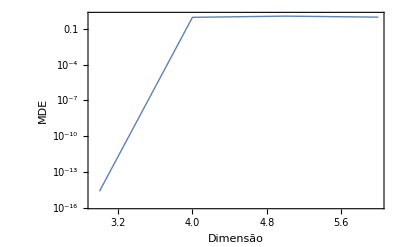

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
Print["\n - - - Abordagem via AGC - - - "];
For[n=3,n≤6,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};
For[jj=1,jj≤1,jj++,eerro=IntersEsferasAGC[n,m,kk,e0,einf,True];
Terros=AppendTo[Terros,eerro];];
];
Print["erro = ",Style[Mean[Terros],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
];

(*plota grafico erros*)
Print[];
ListLogPlot[ListaMedias,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{"Dimensão","MDE"},FrameStyle->Directive[Black,FontSize->13]]
```

- - - Abordagem via álgebra linear - - -

________ m = 3, n = 3 ________

A = (3.90136 | 2.00763 | 4.21633
0.447683 | 0.0433326 | 0.349853
2.62165 | 1.45208 | 2.90708)  d = (2.66698
1.6429
3.08204)

erro = 4.50515×10^-17

______________________________

________ m = 4, n = 4 ________

A = (3.90254 | 2.10451 | 5.69087 | 2.71275
0.449824 | 0.219446 | 3.03019 | 2.75676
2.62402 | 1.64722 | 5.877 | 3.76752
2.40872 | 0.647672 | 2.76247 | 1.33933)  d = (2.42627
3.16714
4.83521
2.17203)

erro = 4.59224×10^-17

______________________________

________ m = 5, n = 5 ________

A = (3.90316 | 2.10688 | 5.69214 | 2.7152 | 4.10342
0.50135 | 0.414118 | 3.13452 | 2.95793 | 0.901832
3.40821 | 4.61002 | 7.46476 | 6.82922 | 5.51096
3.17644 | 3.54823 | 4.31687 | 4.3367 | 3.89355
2.84951 | 1.62747 | 6.54341 | 5.12416 | 3.10694)  d = (3.17137
4.43908
5.63444
4.17504
3.77177)

erro = 7.15432×10^-17

______________________________

________ m = 6, n = 6 ________

A = (3.90483 | 2.10829 | 5.69339 | 2.7165 | 4.10526 | 6.60742
0.507659 | 0.419441 | 3.13923 | 2.96287 | 0.908792 | 2.8852
3.41159 | 4.61287 | 7.46728 | 6.83186 | 5.51469 | 8.3568
3.18296 | 3.55373 | 4.32174 | 4.3418 | 3.90074 | 5.6589
2.85426 | 1.63147 | 6.54695 | 5.12787 | 3.11217 | 6.93323
2.99543 | 4.84349 | 7.64603 | 6.40161 | 5.93712 | 8.17819)  d = (3.72212
5.43691
7.0364
5.35254
5.07573
8.49081)

erro = 3.13418×10^-16

______________________________

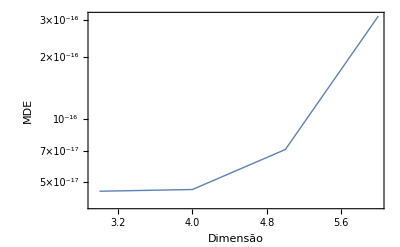

```mathematica
(* executa testes - abordagem clássica *)
ListaMedias={};
ListaTempos={};
Print["\n - - - Abordagem via álgebra linear - - - "];
For[n=3,n≤6,n++,
If[Mod[n,10]==0,
WriteString["stdout",n,"-"]; (* exibe iteração atual *)];
m=n;kk=m-1;
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};
For[jj=1,jj≤1,jj++,eerro=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];];];
Print["erro = ",Style[Mean[Terros][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros[[;;,2]]]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];];

(*plota grafico erros*)
ListLogPlot[ListaMedias,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{"Dimensão","MDE"},FrameStyle->Directive[Black,FontSize->13]]

(*(*plota grafico tempo*)
ListLogPlot[ListaTempos,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{Dimensão,Tempo[s]},FrameStyle->Directive[Black,FontSize->13]]*)
```

### Teste 2 (iniciando com n=3, após reiniciar o Kernel e recarregar módulos):

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
ListaMedias2={};
ListaTempos2={};
For[n=3,n≤6,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};Terros2={};
For[jj=1,jj≤1,jj++,
eerro=IntersEsferasAGC[n,m,kk,e0,einf,False];
eerro2=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];
Terros2=AppendTo[Terros2,eerro2];
];
];
Print["erro AGC = ",Style[Mean[Terros],Red]];
Print["erro Alg.Lin. = ",Style[Mean[Terros2][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
ListaMedias2=AppendTo[ListaMedias2,{m,Mean[Terros2[[;;,2]]]}];
ListaTempos2=AppendTo[ListaTempos2,{m,t}];

];
```

3-4-5-6-

________ m = 3, n = 3 ________

A = (3.90136 | 2.00763 | 4.21633
0.447683 | 0.0433326 | 0.349853
2.62165 | 1.45208 | 2.90708)  d = (2.66698
1.6429
3.08204)

erro AGC = 2.4576×10^-15

erro Alg.Lin. = 4.50515×10^-17

______________________________

________ m = 4, n = 4 ________

A = (3.90254 | 2.10451 | 5.69087 | 2.71275
0.449824 | 0.219446 | 3.03019 | 2.75676
2.62402 | 1.64722 | 5.877 | 3.76752
2.40872 | 0.647672 | 2.76247 | 1.33933)  d = (2.42627
3.16714
4.83521
2.17203)

erro AGC = 0.897712

erro Alg.Lin. = 4.59224×10^-17

______________________________

________ m = 5, n = 5 ________

A = (3.90316 | 2.10688 | 5.69214 | 2.7152 | 4.10342
0.50135 | 0.414118 | 3.13452 | 2.95793 | 0.901832
3.40821 | 4.61002 | 7.46476 | 6.82922 | 5.51096
3.17644 | 3.54823 | 4.31687 | 4.3367 | 3.89355
2.84951 | 1.62747 | 6.54341 | 5.12416 | 3.10694)  d = (3.17137
4.43908
5.63444
4.17504
3.77177)

erro AGC = 1.13418

erro Alg.Lin. = 7.15432×10^-17

______________________________

________ m = 6, n = 6 ________

A = (3.90483 | 2.10829 | 5.69339 | 2.7165 | 4.10526 | 6.60742
0.507659 | 0.419441 | 3.13923 | 2.96287 | 0.908792 | 2.8852
3.41159 | 4.61287 | 7.46728 | 6.83186 | 5.51469 | 8.3568
3.18296 | 3.55373 | 4.32174 | 4.3418 | 3.90074 | 5.6589
2.85426 | 1.63147 | 6.54695 | 5.12787 | 3.11217 | 6.93323
2.99543 | 4.84349 | 7.64603 | 6.40161 | 5.93712 | 8.17819)  d = (3.72212
5.43691
7.0364
5.35254
5.07573
8.49081)

erro AGC = 0.929422

erro Alg.Lin. = 3.13418×10^-16

______________________________

### Teste 3 (iniciando com n=4, após reiniciar o Kernel e recarregar módulos):

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
ListaMedias2={};
ListaTempos2={};

For[n=4,n≤4,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};Terros2={};
For[jj=1,jj≤1,jj++,
eerro=IntersEsferasAGC[n,m,kk,e0,einf,False];
eerro2=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];
Terros2=AppendTo[Terros2,eerro2];
];
];
Print["erro AGC = ",Style[Mean[Terros],Red]];
Print["erro Alg.Lin. = ",Style[Mean[Terros2][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
ListaMedias2=AppendTo[ListaMedias2,{m,Mean[Terros2[[;;,2]]]}];
ListaTempos2=AppendTo[ListaTempos2,{m,t}];

];
```

4-

________ m = 4, n = 4 ________

A = (3.90254 | 2.10451 | 5.69087 | 2.71275
0.449824 | 0.219446 | 3.03019 | 2.75676
2.62402 | 1.64722 | 5.877 | 3.76752
2.40872 | 0.647672 | 2.76247 | 1.33933)  d = (2.42627
3.16714
4.83521
2.17203)

erro AGC = 6.80557×10^-15

erro Alg.Lin. = 4.59224×10^-17

______________________________

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
ListaMedias2={};
ListaTempos2={};

For[n=3,n≤3,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};Terros2={};
For[jj=1,jj≤1,jj++,
eerro=IntersEsferasAGC[n,m,kk,e0,einf,False];
eerro2=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];
Terros2=AppendTo[Terros2,eerro2];
];
];
Print["erro AGC = ",Style[Mean[Terros],Red]];
Print["erro Alg.Lin. = ",Style[Mean[Terros2][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
ListaMedias2=AppendTo[ListaMedias2,{m,Mean[Terros2[[;;,2]]]}];
ListaTempos2=AppendTo[ListaTempos2,{m,t}];

];
```

3-

________ m = 3, n = 3 ________

A = (3.90136 | 2.00763 | 4.21633
0.447683 | 0.0433326 | 0.349853
2.62165 | 1.45208 | 2.90708)  d = (2.66698
1.6429
3.08204)

erro AGC = 0.812624

erro Alg.Lin. = 4.50515×10^-17

______________________________

### Teste 4 (iniciando com n=5, após reiniciar o Kernel e recarregar módulos):

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
ListaMedias2={};
ListaTempos2={};

For[n=5,n≤5,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};Terros2={};
For[jj=1,jj≤1,jj++,
eerro=IntersEsferasAGC[n,m,kk,e0,einf,False];
eerro2=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];
Terros2=AppendTo[Terros2,eerro2];
];
];
Print["erro AGC = ",Style[Mean[Terros],Red]];
Print["erro Alg.Lin. = ",Style[Mean[Terros2][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
ListaMedias2=AppendTo[ListaMedias2,{m,Mean[Terros2[[;;,2]]]}];
ListaTempos2=AppendTo[ListaTempos2,{m,t}];

];
```

5-

________ m = 5, n = 5 ________

A = (3.90316 | 2.10688 | 5.69214 | 2.7152 | 4.10342
0.50135 | 0.414118 | 3.13452 | 2.95793 | 0.901832
3.40821 | 4.61002 | 7.46476 | 6.82922 | 5.51096
3.17644 | 3.54823 | 4.31687 | 4.3367 | 3.89355
2.84951 | 1.62747 | 6.54341 | 5.12416 | 3.10694)  d = (3.17137
4.43908
5.63444
4.17504
3.77177)

erro AGC = 1.14167×10^-13

erro Alg.Lin. = 7.15432×10^-17

______________________________

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
ListaMedias2={};
ListaTempos2={};

For[n=3,n≤3,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};Terros2={};
For[jj=1,jj≤1,jj++,
eerro=IntersEsferasAGC[n,m,kk,e0,einf,False];
eerro2=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];
Terros2=AppendTo[Terros2,eerro2];
];
];
Print["erro AGC = ",Style[Mean[Terros],Red]];
Print["erro Alg.Lin. = ",Style[Mean[Terros2][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
ListaMedias2=AppendTo[ListaMedias2,{m,Mean[Terros2[[;;,2]]]}];
ListaTempos2=AppendTo[ListaTempos2,{m,t}];

];
```

3-

________ m = 3, n = 3 ________

A = (3.90136 | 2.00763 | 4.21633
0.447683 | 0.0433326 | 0.349853
2.62165 | 1.45208 | 2.90708)  d = (2.66698
1.6429
3.08204)

erro AGC = 2.02164

erro Alg.Lin. = 4.50515×10^-17

______________________________

### Teste 5 (iniciando com n=6, após reiniciar o Kernel e recarregar módulos):

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
ListaMedias2={};
ListaTempos2={};

For[n=6,n≤6,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};Terros2={};
For[jj=1,jj≤1,jj++,
eerro=IntersEsferasAGC[n,m,kk,e0,einf,False];
eerro2=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];
Terros2=AppendTo[Terros2,eerro2];
];
];
Print["erro AGC = ",Style[Mean[Terros],Red]];
Print["erro Alg.Lin. = ",Style[Mean[Terros2][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
ListaMedias2=AppendTo[ListaMedias2,{m,Mean[Terros2[[;;,2]]]}];
ListaTempos2=AppendTo[ListaTempos2,{m,t}];

];
```

6-

________ m = 6, n = 6 ________

A = (3.90483 | 2.10829 | 5.69339 | 2.7165 | 4.10526 | 6.60742
0.507659 | 0.419441 | 3.13923 | 2.96287 | 0.908792 | 2.8852
3.41159 | 4.61287 | 7.46728 | 6.83186 | 5.51469 | 8.3568
3.18296 | 3.55373 | 4.32174 | 4.3418 | 3.90074 | 5.6589
2.85426 | 1.63147 | 6.54695 | 5.12787 | 3.11217 | 6.93323
2.99543 | 4.84349 | 7.64603 | 6.40161 | 5.93712 | 8.17819)  d = (3.72212
5.43691
7.0364
5.35254
5.07573
8.49081)

erro AGC = 7.67947×10^-11

erro Alg.Lin. = 3.13418×10^-16

______________________________

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
ListaMedias2={};
ListaTempos2={};

For[n=3,n≤3,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};Terros2={};
For[jj=1,jj≤1,jj++,
eerro=IntersEsferasAGC[n,m,kk,e0,einf,False];
eerro2=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];
Terros2=AppendTo[Terros2,eerro2];
];
];
Print["erro AGC = ",Style[Mean[Terros],Red]];
Print["erro Alg.Lin. = ",Style[Mean[Terros2][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
ListaMedias2=AppendTo[ListaMedias2,{m,Mean[Terros2[[;;,2]]]}];
ListaTempos2=AppendTo[ListaTempos2,{m,t}];

];
```

3-

________ m = 3, n = 3 ________

A = (3.90136 | 2.00763 | 4.21633
0.447683 | 0.0433326 | 0.349853
2.62165 | 1.45208 | 2.90708)  d = (2.66698
1.6429
3.08204)

erro AGC = 2.02164

erro Alg.Lin. = 4.50515×10^-17

______________________________

### Teste 6 (iniciando com n=8, após reiniciar o Kernel e recarregar módulos):

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
ListaMedias2={};
ListaTempos2={};

For[n=8,n≤8,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};Terros2={};
For[jj=1,jj≤1,jj++,
eerro=IntersEsferasAGC[n,m,kk,e0,einf,False];
eerro2=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];
Terros2=AppendTo[Terros2,eerro2];
];
];
Print["erro AGC = ",Style[Mean[Terros],Red]];
Print["erro Alg.Lin. = ",Style[Mean[Terros2][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
ListaMedias2=AppendTo[ListaMedias2,{m,Mean[Terros2[[;;,2]]]}];
ListaTempos2=AppendTo[ListaTempos2,{m,t}];

];
```

8-

________ m = 8, n = 8 ________

A = (3.95744 | 3.20172 | 6.13521 | 3.22872 | 6.02463 | 7.0781 | 4.88108 | 8.23792
2.34154 | 4.93539 | 4.62259 | 6.67482 | 3.93789 | 5.06206 | 2.34979 | 4.5412
4.17169 | 6.87744 | 8.24481 | 8.53572 | 7.51698 | 9.42542 | 6.21124 | 7.86507
3.99622 | 5.95918 | 5.1464 | 6.15747 | 6.00976 | 6.79484 | 6.14553 | 5.45707
6.22932 | 9.4983 | 9.09288 | 11.7723 | 7.84224 | 10.7513 | 5.92289 | 9.5394
3.78664 | 7.28855 | 8.49175 | 8.21218 | 8.18828 | 9.32773 | 5.22447 | 7.46316
3.72293 | 7.13662 | 5.22876 | 5.05757 | 7.18138 | 6.20394 | 3.0695 | 4.4442
6.7063 | 11.1182 | 10.0747 | 10.0085 | 11.5004 | 12.1545 | 7.78504 | 9.1761)  d = (6.61974
8.42622
7.53345
8.72533
8.52462
10.1277
6.16096
6.62853)

erro AGC = 2.36×10^-9

erro Alg.Lin. = 1.04907×10^-16

______________________________

```mathematica
(* executa testes - abordagem AGC *)
ListaMedias={};
ListaTempos={};
ListaMedias2={};
ListaTempos2={};

For[n=3,n≤3,n++,
WriteString["stdout",n,"-"];(* exibe iteração atual *)
m=n;kk=m-1;
(* define assinatura de R^(p,q) e base nula {Subscript[e, 0], Subscript[e, ∞]} *)
$SetSignature=n+1;
p=n+1;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
Print["\n\n________ m = ",m,", n = ",n," ________"];
t=TimeUsed[Terros={};Terros2={};
For[jj=1,jj≤1,jj++,
eerro=IntersEsferasAGC[n,m,kk,e0,einf,False];
eerro2=IntersEsferas[n,m,kk,True];
Terros=AppendTo[Terros,eerro];
Terros2=AppendTo[Terros2,eerro2];
];
];
Print["erro AGC = ",Style[Mean[Terros],Red]];
Print["erro Alg.Lin. = ",Style[Mean[Terros2][[2]],Red]];
Print["______________________________"];
ListaMedias=AppendTo[ListaMedias,{m,Mean[Terros]}];
ListaTempos=AppendTo[ListaTempos,{m,t}];
ListaMedias2=AppendTo[ListaMedias2,{m,Mean[Terros2[[;;,2]]]}];
ListaTempos2=AppendTo[ListaTempos2,{m,t}];

];
```

3-

________ m = 3, n = 3 ________

A = (3.90136 | 2.00763 | 4.21633
0.447683 | 0.0433326 | 0.349853
2.62165 | 1.45208 | 2.90708)  d = (2.66698
1.6429
3.08204)

erro AGC = 2.02164

erro Alg.Lin. = 4.50515×10^-17

______________________________